```mathematica
California=GeoGraphics[{GeoStyling["ReliefMap"],EdgeForm[Black],FaceForm[Red],Polygon[LinguisticAssistant]},(*GeoBackground->None,*)Frame->True]
```

-Graphics-

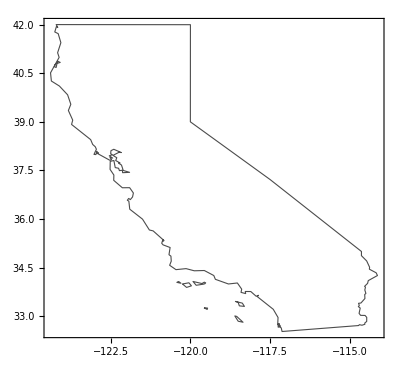

```mathematica
q=Graphics[{FaceForm[],EdgeForm[Directive[Black,Opacity[.7]]],EntityValue[LinguisticAssistant,"Polygon"]},Frame->True]
```

```mathematica
SetDirectory["/Users/penn/Documents/Code/Github/My_Lib/Project/Introduction"];
```

```mathematica
y=Import["average_p.mat"];
```

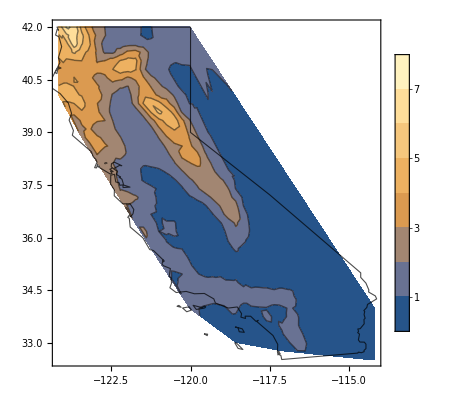

```mathematica
Show[ListContourPlot[y,PlotLegends->Automatic],q]
```

```mathematica
ListDensityPlot[{{-124,36,2},{-114,42,3},{-118,39,3},{-120,38,1}},Epilog->{FaceForm[],EdgeForm[Opacity[0.5]],q}]
```

-Graphics-

```mathematica
qq=EntityValue[LinguisticAssistant,"Polygon"]
```

Polygon[GeoPosition[{{{34.0495,-120.424},{34.0766,-120.368},{34.0219,-120.296},{34.0494,-120.424},{34.0495,-120.424}},{{32.7188,-114.72},{32.535,-117.124},{32.648,-117.15},{32.6818,-117.224},{32.6966,-117.171},{32.7409,-117.208},{32.6664,-117.245},{32.7562,-117.253},{32.7706,-117.208},{32.7583,-117.26},{32.9664,-117.25},{33.2193,-117.4},{33.61,-117.901},{33.6511,-117.867},{33.6215,-117.937},{33.7671,-118.105},{33.7691,-118.279},{33.7038,-118.266},{33.7411,-118.412},{33.8408,-118.391},{34.0308,-118.526},{34.0002,-118.807},{34.1438,-119.216},{34.2608,-119.266},{34.4152,-119.563},{34.4069,-119.878},{34.4734,-120.136},{34.4422,-120.453},{34.5768,-120.651},{34.7046,-120.601},{34.8583,-120.61},{34.9028,-120.672},{35.1246,-120.636},{35.2061,-120.857},{35.2552,-120.9},{35.368,-120.863},{35.3113,-120.867},{35.3382,-120.828},{35.6369,-121.169},{35.6649,-121.287},{35.9991,-121.502},{36.3061,-121.903},{36.5544,-121.931},{36.5815,-121.979},{36.6374,-121.936},{36.6013,-121.884},{36.683,-121.815},{36.8049,-121.788},{36.9691,-121.906},{36.9669,-122.135},{37.1959,-122.405},{37.3594,-122.401},{37.5334,-122.52},{37.7811,-122.515},{37.8073,-122.4},{37.5888,-122.358},{37.5681,-122.253},{37.4946,-122.226},{37.5062,-122.134},{37.4315,-122.126},{37.4422,-121.908},{37.5003,-122.107},{37.6676,-122.162},{37.7243,-122.251},{37.7315,-122.208},{37.8058,-122.343},{37.8936,-122.31},{37.9646,-122.429},{38.0582,-122.244},{38.0522,-122.167},{38.1531,-122.404},{38.1101,-122.493},{38.0159,-122.501},{37.9854,-122.447},{37.9514,-122.546},{37.8822,-122.438},{37.8974,-122.525},{37.8366,-122.472},{37.8154,-122.53},{38.0293,-122.926},{38.0389,-122.88},{38.0355,-122.932},{38.0909,-122.932},{37.99,-122.964},{37.9953,-123.024},{38.1545,-122.949},{38.2312,-122.984},{38.3026,-123.065},{38.451,-123.129},{38.9186,-123.728},{39.0514,-123.691},{39.3487,-123.828},{39.5402,-123.751},{39.8327,-123.852},{40.1034,-124.11},{40.2577,-124.361},{40.5104,-124.387},{40.7649,-124.244},{40.7008,-124.267},{40.6747,-124.213},{40.8,-124.183},{40.8314,-124.083},{40.8645,-124.152},{40.7692,-124.239},{40.9874,-124.118},{41.1298,-124.166},{41.4402,-124.063},{41.7184,-124.148},{41.7707,-124.254},{41.9357,-124.204},{41.9091,-124.16},{41.9978,-124.211},{41.9945,-119.999},{38.9996,-120.001},{37.2204,-117.5},{35.0019,-114.633},{34.8729,-114.634},{34.71,-114.47},{34.5165,-114.378},{34.4562,-114.385},{34.345,-114.173},{34.2604,-114.131},{34.1035,-114.42},{34.0193,-114.441},{33.9275,-114.536},{33.9038,-114.508},{33.815,-114.528},{33.7079,-114.494},{33.6751,-114.532},{33.5522,-114.525},{33.4136,-114.65},{33.4041,-114.726},{33.337,-114.701},{33.3024,-114.731},{33.2585,-114.672},{33.094,-114.708},{33.0327,-114.66},{33.03,-114.52},{32.9707,-114.468},{32.8452,-114.469},{32.7955,-114.53},{32.7571,-114.527},{32.7283,-114.617},{32.7456,-114.702},{32.7188,-114.72}},{{33.,-118.548},{32.8205,-118.349},{32.8515,-118.5},{33.0147,-118.607},{33.0009,-118.548},{33.,-118.548}},{{33.2671,-119.573},{33.2567,-119.461},{33.2149,-119.474},{33.267,-119.573},{33.2671,-119.573}},{{33.4633,-118.592},{33.4093,-118.371},{33.3087,-118.305},{33.3256,-118.465},{33.4359,-118.501},{33.463,-118.592},{33.4633,-118.592}},{{34.,-120.248},{34.0367,-120.046},{33.9426,-119.968},{33.8944,-120.12},{34.,-120.248}},{{34.,-120.248},{34.,-120.248},{34.0002,-120.248},{34.,-120.248}},{{34.,-119.553},{33.9599,-119.818},{34.0777,-119.918},{34.0132,-119.638},{34.0559,-119.563},{34.0341,-119.52},{34.0002,-119.553},{34.,-119.553}}}]]

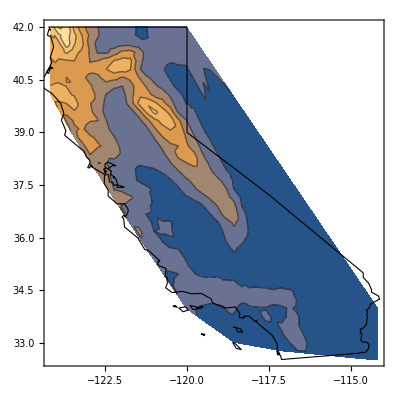

```mathematica
ListContourPlot[y,Epilog->{FaceForm[],EdgeForm[Black],qq}]
```